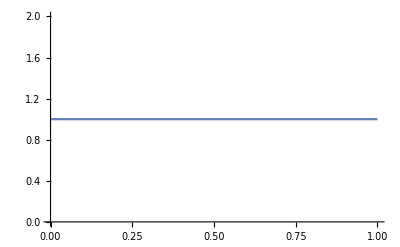

```mathematica
Plot[PDF[BetaDistribution[1, 1], x], {x, 0, 1}]
```

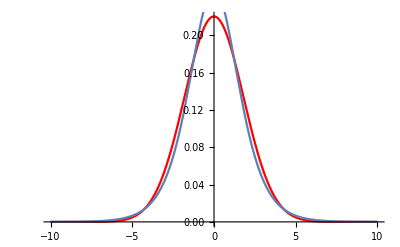

```mathematica
Show[Plot[PDF[NormalDistribution[0, 1.81], x], {x, -10, 10}, PlotStyle->Red],Plot[PDF[BetaDistribution[1, 1], LogisticSigmoid[x]] (1 - LogisticSigmoid[x]) LogisticSigmoid[x], {x, -10, 10}]]
```

```mathematica
rnd = RandomVariate[BetaDistribution[1, 1], 50000000];
data = Log[rnd / (1 - rnd)];
FindDistributionParameters[data, NormalDistribution[μ, σ]]
```

{μ→8.49628×10^-6,σ→1.81368}

```mathematica
trData = 1 / (1 + Exp[-data]);
```

```mathematica
Kurtosis[data]
```

4.20285

```mathematica
Skewness[RandomVariate[NormalDistribution[2, 2], 50000000]]
```

-0.0000452361

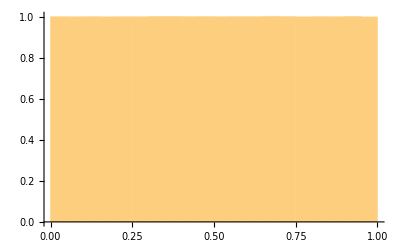

```mathematica
Histogram[trData, Automatic, "PDF"]
```

```mathematica
NIntegrate[x^4 PDF[BetaDistribution[1, 1], LogisticSigmoid[x]] (1 - LogisticSigmoid[x]) LogisticSigmoid[x], {x, -Infinity, Infinity}] / NIntegrate[x^2 PDF[BetaDistribution[1, 1], LogisticSigmoid[x]] (1 - LogisticSigmoid[x]) LogisticSigmoid[x], {x, -Infinity, Infinity}]^2
```

4.2

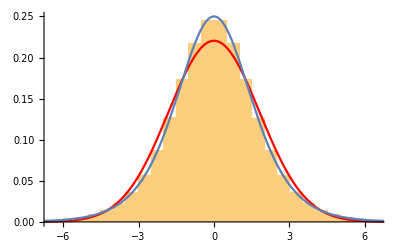

```mathematica
Show[Histogram[data, Automatic, "PDF"], Plot[PDF[NormalDistribution[0, 1.81], x], {x, -10, 10}, PlotStyle->Red],Plot[PDF[BetaDistribution[1, 1], LogisticSigmoid[x]] (1 - LogisticSigmoid[x]) LogisticSigmoid[x], {x, -10, 10}]]
```

```mathematica
Histogram[rnd, Automatic, "PDF"]
```

-Graphics-